## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.1; qscal=1.5;
```

```mathematica
winit=(0.25-0.00005*I)
```

0.25-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+10^(-3);r1=30 ;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

0.251477+0.0000270435 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=M+10^(-3);r1=30; wc=qscal;
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-2*I*M*(wres-wc);
sigmasol=M*(qscal*wres+mu^2-2*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[
{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (wres*r^2-qscal*M*r)^2/(r-M)^4 - 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(wres-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(wres-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(wres-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

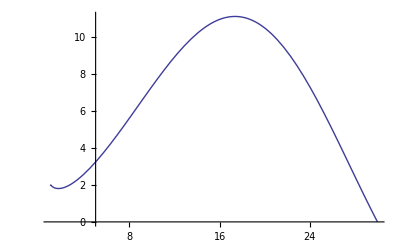

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,r0,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.25-0.00005*I);
ie=0;While[ie<101,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=30 +ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);

sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,100}];
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,100}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.25-0.00005*I);
ie=0;While[ie<51,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=30 -ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.0008;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,50}]
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,50}];
```

{{30.,0.251477},{29.8,0.252721},{29.6,0.253982},{29.4,0.255261},{29.2,0.256559},{29.,0.257874},{28.8,0.259209},{28.6,0.260563},{28.4,0.261937},{28.2,0.26333},{28.,0.264744},{27.8,0.266179},{27.6,0.267635},{27.4,0.269113},{27.2,0.270613},{27.,0.272136},{26.8,0.273682},{26.6,0.275252},{26.4,0.276845},{26.2,0.278464},{26.,0.280108},{25.8,0.281777},{25.6,0.283473},{25.4,0.285196},{25.2,0.286947},{25.,0.288725},{24.8,0.290533},{24.6,0.29237},{24.4,0.294237},{24.2,0.296136},{24.,0.298065},{23.8,0.300028},{23.6,0.302023},{23.4,0.304052},{23.2,0.306117},{23.,0.308216},{22.8,0.310353},{22.6,0.312526},{22.4,0.314738},{22.2,0.31699},{22.,0.319281},{21.8,0.321614},{21.6,0.32399},{21.4,0.326409},{21.2,0.328873},{21.,0.331382},{20.8,0.333938},{20.6,0.336543},{20.4,0.339198},{20.2,0.341903},{20.,0.344661}}

```mathematica
winit=(0.35-0.00005*I);
ie=0;While[ie<26,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=20 -ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l2=Table[{N[radit[n],10],Re[witer[n]]},{n,0,25}]
t2l2=Table[{N[radit[n],10],Im[witer[n]]},{n,0,25}];
```

{{20.,0.344661},{19.8,0.347473},{19.6,0.35034},{19.4,0.353263},{19.2,0.356246},{19.,0.359289},{18.8,0.362393},{18.6,0.365562},{18.4,0.368796},{18.2,0.372097},{18.,0.375469},{17.8,0.378912},{17.6,0.382429},{17.4,0.386022},{17.2,0.389694},{17.,0.393448},{16.8,0.397285},{16.6,0.401208},{16.4,0.405221},{16.2,0.409325},{16.,0.413525},{15.8,0.417824},{15.6,0.422224},{15.4,0.42673},{15.2,0.431344},{15.,0.436071}}

```mathematica
winit=(0.45-0.00005*I);
ie=0;While[ie<26,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=15 -ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.0008;
ie=ie+1

]
t1l3=Table[{N[radit[n],10],Re[witer[n]]},{n,0,25}]
t2l3=Table[{N[radit[n],10],Im[witer[n]]},{n,0,25}];
```

{{15.,0.436071},{14.8,0.440915},{14.6,0.44588},{14.4,0.450969},{14.2,0.456189},{14.,0.461544},{13.8,0.467038},{13.6,0.472677},{13.4,0.478466},{13.2,0.484412},{13.,0.490521},{12.8,0.496798},{12.6,0.503251},{12.4,0.509886},{12.2,0.516713},{12.,0.523737},{11.8,0.530968},{11.6,0.538414},{11.4,0.546085},{11.2,0.55399},{11.,0.562141},{10.8,0.570547},{10.6,0.579221},{10.4,0.588175},{10.2,0.597421},{10.,0.606974}}

```mathematica
winit=(0.6-0.00005*I);
ie=0;While[ie<31,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=10 -ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.0008;
ie=ie+1

]
t1l4=Table[{N[radit[n],10],Re[witer[n]]},{n,0,30}]
t2l4=Table[{N[radit[n],10],Im[witer[n]]},{n,0,30}]
```

{{10.,0.606974},{9.8,0.616849},{9.6,0.62706},{9.4,0.637625},{9.2,0.64856},{9.,0.659885},{8.8,0.671619},{8.6,0.683783},{8.4,0.6964},{8.2,0.709494},{8.,0.723089},{7.8,0.737212},{7.6,0.751893},{7.4,0.767161},{7.2,0.783049},{7.,0.79959},{6.8,0.816822},{6.6,0.834781},{6.4,0.853509},{6.2,0.873047},{6.,0.893439},{5.8,0.914731},{5.6,0.936969},{5.4,0.960201},{5.2,0.984472},{5.,1.00983},{4.8,1.03631},{4.6,1.06395},{4.4,1.09278},{4.2,1.12281},{4.,1.15402}}

{{10.,0.000225435},{9.8,0.000230439},{9.6,0.000235354},{9.4,0.000240492},{9.2,0.000245575},{9.,0.000250584},{8.8,0.000255883},{8.6,0.000260972},{8.4,0.000266193},{8.2,0.000271325},{8.,0.000276499},{7.8,0.000281547},{7.6,0.000286319},{7.4,0.000291225},{7.2,0.000295745},{7.,0.000300301},{6.8,0.000304402},{6.6,0.000307958},{6.4,0.000311272},{6.2,0.000314258},{6.,0.000316402},{5.8,0.000317782},{5.6,0.00031842},{5.4,0.00031792},{5.2,0.000315992},{5.,0.000312961},{4.8,0.000308183},{4.6,0.000301563},{4.4,0.000292952},{4.2,0.000281919},{4.,0.00026809}}

```mathematica
winit=(1.15-0.00005*I);
ie=0;While[ie<7,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=4 -ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l5=Table[{N[radit[n],10],Re[witer[n]]},{n,0,5}]
t2l5=Table[{N[radit[n],10],Im[witer[n]]},{n,0,5}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{4.,1.15402},{3.8,1.18637},{3.6,1.21977},{3.4,1.25406},{3.2,1.28899},{3.,1.32419}}

{{4.,0.00026809},{3.8,0.000251},{3.6,0.000231444},{3.4,0.000208311},{3.2,0.00018186},{3.,0.000152681}}

```mathematica
(*The imaginary part vs the radius*)
```

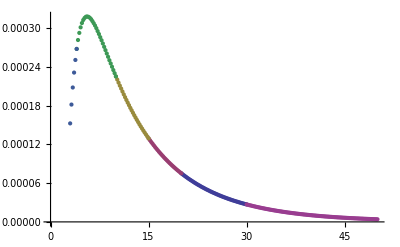

```mathematica
ListPlot[{t2l,t2l2,t2l3,t2l4,t2l5,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

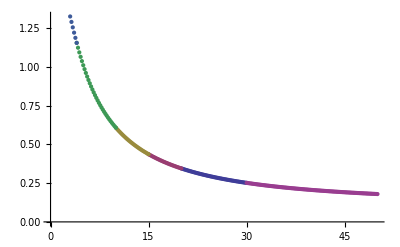

```mathematica
ListPlot[{t1l,t1l2,t1l3,t1l4,t1l5,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=1.0/q=1.5/R.dat",Join[t1l,t1l2,t1l3,t1l4,t1l5,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=1.0/q=1.5/I.dat",Join[t2l,t2l2,t2l3,t2l4,t2l5,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=1.0/q=1.5/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=1.0/q=1.5/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-M^2]
rm=M-Sqrt[M^2-M^2]
rmirror=40
```

1

1

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*M/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.3

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```